```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
gears=Import["/Users/ant/Sites/JumpStartIM/assets/images/functions/gearsanim.gif"];
gears[[1]]
```

-Graphics-

```mathematica
Show[
Graphics[{EdgeForm[Black],PatternFilling[gears[[1]]],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style["Input:\nCivic",18],{-1.5,1/2}],Text[Style["Output:\nHonda",18],{2.5,1/2}]}
]
Export[{"function2.svg","function2.pdf"},%];
```

-Graphics-

```mathematica
Show[
Graphics[{EdgeForm[Black],PatternFilling[gears[[1]]],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style["Input:\nHonda",18],{-1.5,1/2}],Text[Style["Output:\n????",18],{2.5,1/2}]}
]
Export[{"function3.svg","function3.pdf"},%];
```

-Graphics-

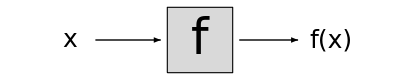

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[HoldForm[f],50],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f[x]]],25],{2.5,1/2}]}
]
Export[{"function4.svg","function4.pdf"},%];
```

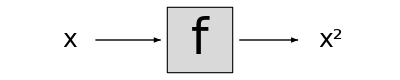

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[HoldForm[f],50],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[x^2]],25],{2.5,1/2}]}
]
Export[{"function5.svg","function5.pdf"},%];
```

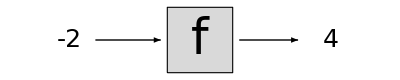

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[-2],25],{-1.5,1/2}],
Text[Style[HoldForm[f],50],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[4]],25],{2.5,1/2}]}
]
Export[{"function6.svg","function6.pdf"},%];
```

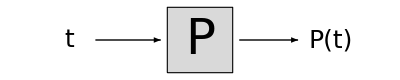

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[t],25],{-1.5,1/2}],
Text[Style[HoldForm[P],50],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[P[t]]],25],{2.5,1/2}]}
]
Export[{"function7.svg","function7.pdf"},%];
```

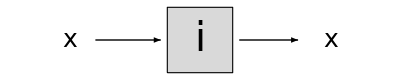

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[HoldForm[i],40],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[x]],25],{2.5,1/2}]}
]
Export[{"identitymap.svg","identitymap.pdf"},%];
```

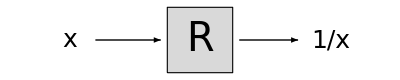

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[HoldForm[R],40],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[1/x]],25],{2.5,1/2}]}
]
Export[{"reciprocalmap.svg","reciprocalmap.pdf"},%];
```

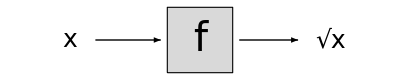

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[HoldForm[f],40],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[Sqrt[x]]],25],{2.5,1/2}]}
]
Export[{"sqrtmap.svg","sqrtmap.pdf"},%];
```

```mathematica
Quit[]
```

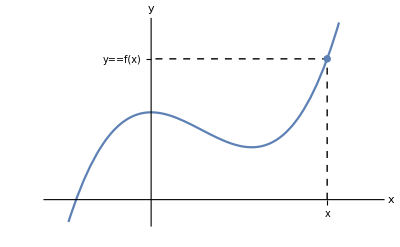

{graphing-function-general.svg,graphing-function-general.pdf}

```mathematica
f[x_]:=x^3-3x^2+10
Show[
Plot[f[x],{x,-2,4.5},Ticks->{{{3.5,x}},{{f[3.5],HoldForm[y==f[x]]}}}],
Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],
ListPlot[{{3.5,f[3.5]}}],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y}]
Export[{"graphing-function-general.svg","graphing-function-general.pdf"},%]
```

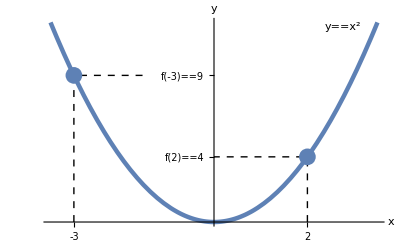

{graphing-function-squaring.svg,graphing-function-squaring.pdf}

```mathematica
f[x_]:=x^2
Show[
Plot[f[x],{x,-3.5,3.5},PlotStyle->{Thickness[0.008]},Ticks->{{2,-3},{{f[2],HoldForm[f[2]==4]},{f[-3],HoldForm[f[-3]==9]}}}],
Graphics[{Dashed,Line[{{2,0},{2,f[2]},{0,f[2]}}]}],
Graphics[{Dashed,Line[{{-3,0},{-3,f[-3]},{-1.5,f[-3]}}]}],
ListPlot[{{2,f[2]},{-3,f[-3]}},PlotStyle->PointSize[0.03]],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y},
Epilog->{{Style[Text[HoldForm[y==x^2],{2.75,12}],FontSize->16]}}
]
Export[{"graphing-function-squaring.svg","graphing-function-squaring.pdf"},%]
```

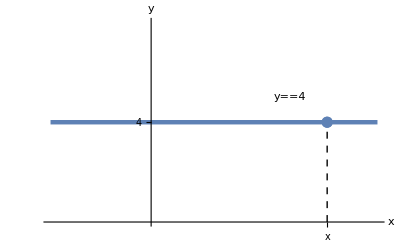

{graphing-function-constant.svg,graphing-function-constant.pdf}

```mathematica
f[x_]:=4
Show[
Plot[f[x],{x,-2,4.5},PlotStyle->{Thickness[0.008]},Ticks->{{{3.5,x}},{4}}],
Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]}}]}],
ListPlot[{{3.5,f[3.5]}},PlotStyle->PointSize[0.02]],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y},Epilog->{{Style[Text[HoldForm[y==4],{2.75,5}],FontSize->16]}}
]
Export[{"graphing-function-constant.svg","graphing-function-constant.pdf"},%]
```

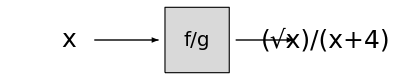

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{0,1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f/g]],20],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[Sqrt[x]/(x+4)]],25],{2.5,1/2}]}
]
Export[{"ratiomap.svg","ratiomap.pdf"},%];
```

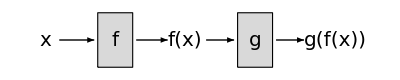

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{EdgeForm[Black],LightGray,Rectangle[{4,0},{5,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
Graphics[{Arrow[{{3.1,1/2},{3.9,1/2}}]}],
Graphics[{Arrow[{{5.1,1/2},{5.9,1/2}}]}],
PlotRange->{{-1.75,7.6},{-0.1,1.1}},
Epilog->{Text[Style[HoldForm[x],20],{-1.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f]],20],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[g]],20],{4.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f[x]]],20],{2.5,1/2}],
Text[Style[TraditionalForm[HoldForm[g[f[x]]]],20],{6.8,1/2}]}
]
Export[{"compmap.svg","compmap.pdf"},%];
```

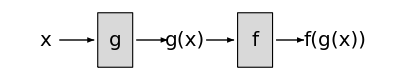

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{EdgeForm[Black],LightGray,Rectangle[{4,0},{5,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
Graphics[{Arrow[{{3.1,1/2},{3.9,1/2}}]}],
Graphics[{Arrow[{{5.1,1/2},{5.9,1/2}}]}],
PlotRange->{{-1.75,7.6},{-0.1,1.1}},
Epilog->{Text[Style[HoldForm[x],20],{-1.5,1/2}],
Text[Style[TraditionalForm[HoldForm[g]],20],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f]],20],{4.5,1/2}],
Text[Style[TraditionalForm[HoldForm[g[x]]],20],{2.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f[g[x]]]],20],{6.8,1/2}]}
]
Export[{"compmap2.svg","compmap2.pdf"},%];
```

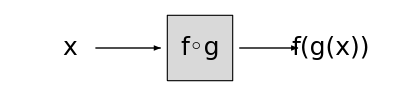

```mathematica
Show[
Graphics[{EdgeForm[Black],LightGray,Rectangle[{0,0},{1,1}]}],
Graphics[{Arrow[{{-1.1,1/2},{-0.1,1/2}}]}],
Graphics[{Arrow[{{1.1,1/2},{2,1/2}}]}],
PlotRange->{{-2,3},{-.1,1.1}},
Epilog->{Text[Style[HoldForm[x],25],{-1.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f◦g]],25],{0.5,1/2}],
Text[Style[TraditionalForm[HoldForm[f[g[x]]]],25],{2.5,1/2}]}
]
Export[{"compmapcirc.svg","compmapcirc.pdf"},%];
```

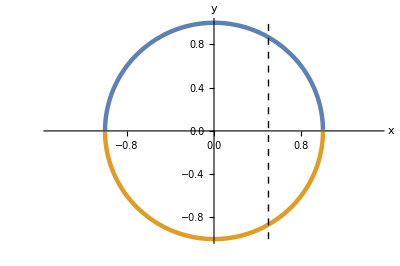

{circle.pdf,circle.svg}

```mathematica
Show[
Plot[{Sqrt[1-x^2],-Sqrt[1-x^2]},{x,-1.5,1.5},PlotStyle->{Thickness[0.008]},AspectRatio->2/3],
Graphics[{Dashed,Line[{{0.5,-10},{0.5,10}}]}],
Ticks->{{-1,1}},
TicksStyle->Directive[12],
AxesStyle->Directive[14],
AxesLabel->{x,y}]
Export[{"circle.pdf","circle.svg"},%]
```

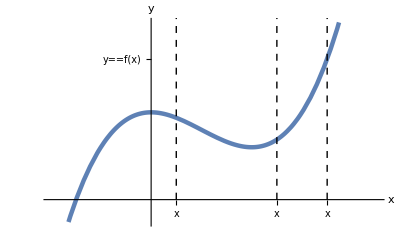

{graphing-function-vertical-line.svg,graphing-function-vertical-line.pdf}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=x^3-3x^2+10
Show[
Plot[f[x],{x,-2,4.5},PlotStyle->{Thickness[0.008]},Ticks->{{{3.5,x},{2.5,x},{0.5,x}},{{f[3.5],HoldForm[y==f[x]]}}}],
(*Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],*)
Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]+10}}]}],
Graphics[{Dashed,Line[{{2.5,0},{2.5,f[2.5]+20}}]}],
Graphics[{Dashed,Line[{{0.5,0},{0.5,f[0.5]+20}}]}],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y}]
Export[{"graphing-function-vertical-line.svg","graphing-function-vertical-line.pdf"},%]
```

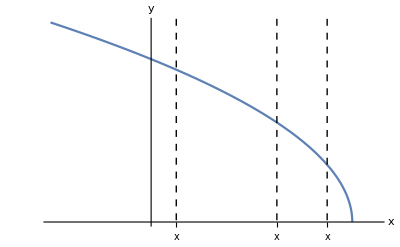

{graphing-function-vertical-line-fail.svg,graphing-function-vertical-line-fail.pdf}

```mathematica
SetDirectory[NotebookDirectory[]];

Show[
Plot[Sqrt[4-x]+5,{x,-2,4.5},Ticks->{{{3.5,x},{2.5,x},{0.5,x}},{{f[3.5],HoldForm[y==f[x]]}}}],
(*Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],*)
Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]+10}}]}],
Graphics[{Dashed,Line[{{2.5,0},{2.5,f[2.5]+20}}]}],
Graphics[{Dashed,Line[{{0.5,0},{0.5,f[0.5]+20}}]}],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y}]
Export[{"graphing-function-vertical-line-fail.svg","graphing-function-vertical-line-fail.pdf"},%]
```